```mathematica
Exit[]
```

```mathematica
$Assumptions=μ>0&&σ>0&&a ∈ Reals&&1>k1≥0&&k0≥0&&S0>0&&K>0&&r≥0&&b ∈ Reals&& rf≥0&& γ>0;
```

```mathematica
ost == σ √t; mpr==(μ-r)/σ^2;
xx[W_,mpr_,ost_]:=Exp[ ost W+(mpr-1/2)ost^2];
Δ[k_]:=1/2(1+Erf[(-Log[k]+ost^2/2)/ost])-1//N
Δ[0.]=0;
```

```mathematica
γ=.1;mpr=0.1;ost=.01;
NIntegrate[xx[w,mpr,ost]Exp[-w^2/2],{w,-∞,∞}]/√(2π)-Exp[mpr ost^2]

pr[f_]:=Log[NIntegrate[Exp[-γ f[xx[w,mpr,ost]]-w^2/2],{w,-∞,∞}]/√(2π)]/-γ;
opt2[f_]:=NIntegrate[Exp[-γ f[xx[w,mpr,ost]]-w^2/2](xx[w,mpr,ost]-1),{w,-∞,∞}];
opt[f_]:=Min[.1,Max[-.1,opt2[f]]]

h[a_]:=a(#-1)&
put[k_,a_]:=h[a][#]-Max[0,k-#]&;
```

-6.54587×10^-13

```mathematica
γ=.1;mpr=0.1;ost=1;arb=Quiet[FindRoot[opt2[h[b]]==0,{b,0,10}][[1,2]]]
hedge[k_]:=If[opt2[put[k,0]]≤ 0,0,FindRoot[opt2[put[k,a]]==0,{a,0,10}][[1,2]]]

plot[kl_]:=Module[{x=Quiet[hedge[#]]&/@kl,y,i=1},
y=Max[x];
Show[ParallelTable[With[{j=i++},
Plot[pr[put[k,a]]-put[k,a][1],{a,0,3 y},
PlotStyle->{ColorData[1,"ColorList"][[j]]}
]],{k,kl}],
PlotRange->All,
Epilog->Flatten[{Directive[{Dashed,Red}],
Table[
{Point[{x[[i]],0}],
Point[{x[[i]],pr[put[kl[[i]],x[[i]]]]-put[kl[[i]],x[[i]]][1]}]}
,{i,Length[kl]}]}]
]]
```

0.621583

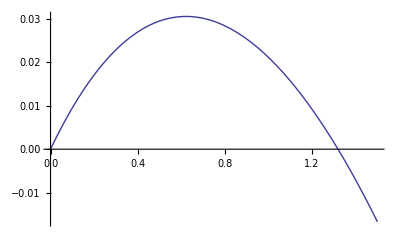

```mathematica
Plot[{pr[h[a]]},{a,0,1.5}]
```

```mathematica
$Assumptions=k≥ 0;
```

```mathematica
f[a_,w_]:=ⅇ^(-a ⅇ^w-w^2)
fc2[n_]:=NIntegrate[(-1)^n/(n!) ⅇ^(-ⅇ^w+n w-w^2),{w,-∞,∞}]
fc=Evaluate[Integrate[SeriesCoefficient[f[a,w],{a,0,k}],{w,-∞,∞}]]
```

((-1)^k ⅇ^(k^2/4) √π)/(k!)

```mathematica
g[a_]:=Log[NIntegrate[f[a,w],{w,-∞,∞}]]
gs[a_,n_]:=Log[Sum[a^k fc/.k-> j,{j,0,n}]]
gs2[a_,k_]:=Log[fc2[0]+Sum[fc2[n](a-1)^n,{n,1,k}]]
```

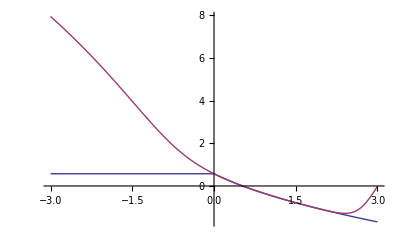

```mathematica
o=-3;p=3;l=Evaluate[gs2[a,10]];Plot[{g[Max[0,a]],l},{a,o,p}]
```

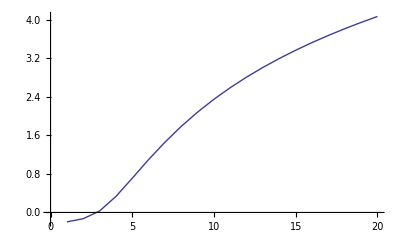

```mathematica
ListLinePlot[Table[Log[Log[Abs[fc]]],{k,1,20}]]
```

```mathematica
fcs=Quiet[Table[fc2[n],{n,650}]];
```

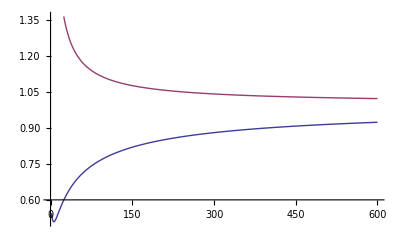

```mathematica
ListLinePlot[Transpose[Table[{Abs[fcs[[n]]]^(1/n),Abs[fcs[[n]]/fcs[[n+1]]]},{n,1,600}]]]
```